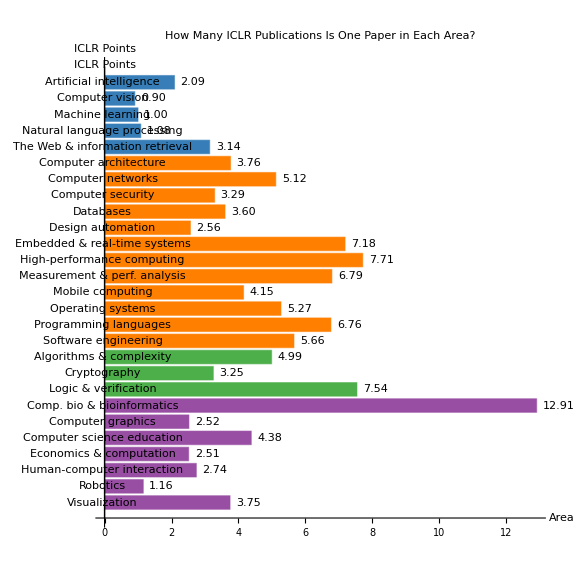

```mathematica
(*Import names.csv and build a mapping:ParentArea->{ReadableTitle,ParentParentArea}*)namesData=Import[FileNameJoin[{NotebookDirectory[],"names.csv"}],"CSV"];
namesData=Rest[namesData];  (*remove header row*)
areaMapping=Association[Table[namesData[[i,1]]->{namesData[[i,2]],namesData[[i,3]]},{i,Length[namesData]}]];

(*Import the publication data*)
data=Import[FileNameJoin[{NotebookDirectory[],"pubs_per_faculty_with_iclr.csv"}],"CSV"];
data=Rest[data];  (*remove header row*)
areas=data[[All,1]];
iclrPoints=ToExpression[data[[All,5]]];

(*Map each ParentArea to its readable title and parent parent area*)
mapped=areaMapping/@areas;
readableTitles=mapped[[All,1]];
parentParent=mapped[[All,2]];

(*Define a unique color for each ParentParentArea*)
colorMapping=<|"AI"->RGBColor[55/255,126/255,184/255],"Systems"->RGBColor[255/255,127/255,0/255],"Theory"->RGBColor[77/255,175/255,74/255],"Interdisciplinary Areas"->RGBColor[152/255,78/255,163/255]|>;
barColors=Lookup[colorMapping,parentParent,Gray];

(*Define desired order for ParentParentArea*)
order={"AI","Systems","Theory","Interdisciplinary Areas"};
sortKey[pp_]:=FirstPosition[order,pp,{Infinity}][[1]];

(*Combine and sort the data based on ParentParentArea order*)
combined=Transpose[{readableTitles,iclrPoints,parentParent,barColors}];
sortedCombined=SortBy[combined,sortKey[#[[3]]]&];
sortedReadable=sortedCombined[[All,1]];
sortedICLRPoints=sortedCombined[[All,2]];
sortedBarColors=sortedCombined[[All,4]];

(*Create a horizontal bar chart*)
BarChart[Reverse@sortedICLRPoints,LabelingFunction->(Placed[NumberForm[#1,{4,2}],After]&),AspectRatio->1,BarOrigin->Left,ChartLabels->Reverse@sortedReadable,ChartStyle->Reverse@sortedBarColors,AxesLabel->{"ICLR Points","Area"},PlotLabel->"How Many ICLR Publications Is One Paper in Each Area?",ImageSize->Large]
```

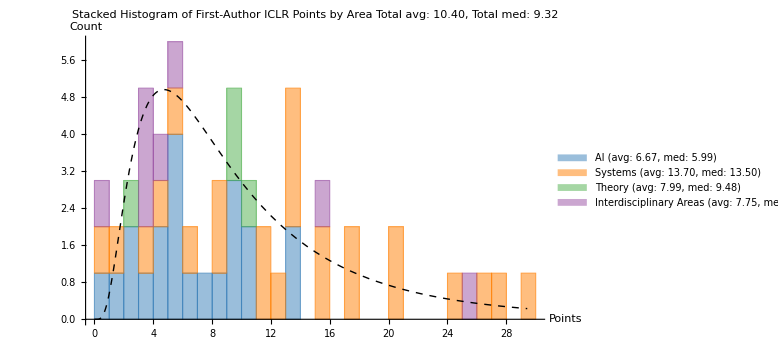

```mathematica
(*Define the desired order and color mapping*)order={"AI","Systems","Theory","Interdisciplinary Areas"};
colorMapping=<|"AI"->RGBColor[55/255,126/255,184/255],"Systems"->RGBColor[255/255,127/255,0/255],"Theory"->RGBColor[77/255,175/255,74/255],"Interdisciplinary Areas"->RGBColor[152/255,78/255,163/255]|>;

(*Import the CSV file;update the path as needed*)
data=Import[FileNameJoin[{NotebookDirectory[],"iclr_points_report.csv"}],"CSV"];
rawData=Rest[data];  (*drop header*)

(*Group data by parent_parent_area (column 5)*)
grouped=GroupBy[rawData,#[[5]]&];

(*Reorder groups using the defined order*)
sortedKeys=Select[order,MemberQ[Keys[grouped],#]&];

(*Extract first-author ICLR points (column 2) for each group in sorted order;
convert them to numbers*)
pointsList=Map[ToExpression/@(#[[2]]&/@#)&,grouped];
sortedPointsList=Lookup[pointsList,sortedKeys];

(*Compute average and median for each area*)
areaAverages=Map[Mean,sortedPointsList];
areaMedians=Map[Median,sortedPointsList];

(*Aggregate data across all areas*)
allData=Flatten[sortedPointsList];
allDataPos=Select[allData,#>0&];  (*for LogNormal fit*)

(*Compute overall average and median*)
totalAvg=Mean[allDataPos];
totalMedian=Median[allDataPos];

(*Generate legend entries for each area including average and median*)
legendEntries=MapThread[#1<>" (avg: "<>ToString[NumberForm[#2,{3,2}]]<>", med: "<>ToString[NumberForm[#3,{3,2}]]<>")"&,{sortedKeys,areaAverages,areaMedians}];

(*Create a stacked histogram with 1-unit bin width and density normalization*)
stackedHistogram=Histogram[sortedPointsList,{1},ChartLayout->"Stacked",ChartLegends->legendEntries,ChartStyle->(Lookup[colorMapping,#,Gray]&/@sortedKeys),AxesLabel->{"Points","Count"},PlotLabel->"Stacked Histogram of First-Author ICLR Points by Area"<>"\nTotal avg: "<>ToString[NumberForm[totalAvg,{3,2}]]<>", Total med: "<>ToString[NumberForm[totalMedian,{3,2}]],ImageSize->Large];

(*Fit a LogNormalDistribution to the aggregated positive data*)
dist=EstimatedDistribution[allDataPos,LogNormalDistribution[μ,σ]];

(*Plot the fitted probability density function (scaled by total count)*)
pdfPlot=Plot[PDF[dist,x]*Length[rawData],{x,Min[allData],Max[allData]},PlotStyle->{Black,Thick,Dashed}];

(*Overlay the fitted PDF onto the stacked histogram*)
Show[stackedHistogram,pdfPlot]
```